# Zbrani in odloženi komunalni odpadki občin v Sloveniji

## Med leti 2012 in 2020

## Zbiranje podatkov

Podatke sem pridobila na spletni strani https://pxweb.stat.si/SiStatData/pxweb/sl/Data/Data/2700020S.px/ in jih uvozila v Mathematico. Podatke sem s pomočjo tega programa uredila in iz tabele odstranila vse nepotrebne vrstice in stolpce. Spodaj je uvožena urejena tabela podatkov, ki predstavlaja vse nastale in odložene komunalne odpadke od leta 2012 do 2020 za vsako občino v Sloveniji. Podatki so izraženi v enoti kilogram/prebivalca. 

Iz tabele je odstranjena vrstica za leto 2016 (odloženi komunalni odpadki), saj za to leto tej podatki niso bili zabeleženi. Druga izjema je občina Ankaran; informacije o komunalnih odpadkih te občine so beležene komaj po letu 2015, saj je občina nastala leta 2011 in podatki, nekaj let po njenem nastanku prav tako niso zbrani in zabeleženi.

```mathematica
dataImport = Import[NotebookDirectory[]<> "2700020S_20220827-160128.csv","Table", FieldSeparators -> ",", HeaderLines -> 3, CharacterEncoding->"WindowsEastEurope"];

vsi= dataImport//Prepend[#,{"Občine", "Nastali - 2012", "Odloženi - 2012",  "Nastali - 2013", "Odloženi - 2013", "Nastali - 2014", "Odloženi - 2014", "Nastali - 2015", "Odloženi - 2015", "Nastali - 2016", "Odloženi - 2016", "Nastali - 2017", "Odloženi - 2017", "Nastali - 2018", "Odloženi - 2018", "Nastali - 2019", "Odloženi - 2019", "Nastali - 2020", "Odloženi - 2020"} ]& //
ResourceFunction["DatasetWithHeaders"] ;

data = vsi [Drop[Range[213], {3}],Drop[Range[19],{11}] ]//Query[All, <|#,"skupaj" -> Total[Drop[#,{1}]]|>&]
(*Izpusti 11 stolpec (leto 2016) in 3 vrstico (Ankaran) ter doda zadnji stolpec kot seštevek vseh stolpcev*)
```

```mathematica
data//Transpose;
nastali = data[All, <|"Občine" -> "Občine" , 2012 ->"Nastali - 2012" ,  2013 ->"Nastali - 2013",  2014 ->"Nastali - 2014",  2015 ->"Nastali - 2015",2016 ->"Nastali - 2016",2017 ->  "Nastali - 2017",2018 -> "Nastali - 2018",2019 -> "Nastali - 2019",  2020 ->"Nastali - 2020"|>]//Query[All,<|#,"Skupaj"->Total[Select[Values[#],NumberQ]]|>&];

odlozeni = data[ All,<|"Občine"-> "Občine",  2012->"Odloženi - 2012", 2013-> "Odloženi - 2013", 2014->  "Odloženi - 2014", 2015-> "Odloženi - 2015",  2017->  "Odloženi - 2017",  2018-> "Odloženi - 2018",  2019-> "Odloženi - 2019"|>]//Query[All,<|#,"Skupaj"->Total[Select[Values[#],NumberQ]]|>&];
```

## Število odpadkov v Sloveniji

```mathematica
NastaliodpadkiSLO = nastali[First]
```

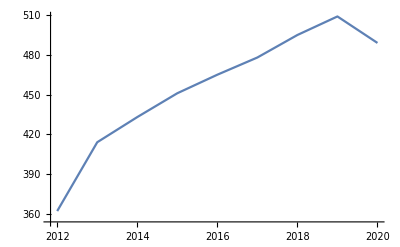

```mathematica
ListLinePlot[NastaliodpadkiSLO]
```

Število nastalih odpadkov v Sloveniji se iz leta v leto povečuje. Številke so nam pokazale, da kljub osveščenosti o globalnem segrevanju in drugih naravnih problemih ljudje neustavljivo uničujemo naš planet. Ustavi nas lahko samo mati narava, kot je iz krivulje razvidno po letu 2019. Po skoraj desetletju je naklon premice o količini nastalih odpadkov prvič negativen. Po pojavitvi prve različice nalezljive bolezni Covid-19 in prvih ukrepih o zmanjšanju druženja in zadrževanju doma,  se je po različnih raziskavah bistveno zmanjšala količina odpadkov v proizvodnji dejavnosti, nekoliko povečala pa količina odpadkov v gospodinjstvih. Ni se zmanjšala samo količina odpadkov temveč je bolezen vse dejavnike onesnaževanja potisnila v kot.

```mathematica
OdloženiodpadkiSLO = odlozeni[First]
```

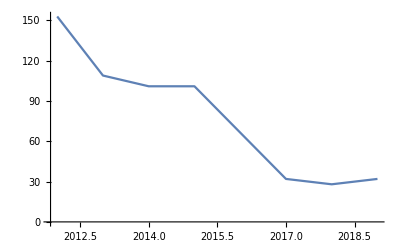

```mathematica
ListLinePlot[OdloženiodpadkiSLO]
```

Krivulja o odloženih odpadkih pa nakazuje na nekoliko bolj svetla in zelena leta za naš planet in sicer se je količina odloženih odpadkov bistveno zmanjšala po sprejeti odredbi o odlaganju odpadkov po letu 2006. Bistveno se je povečala količina ločeno zbranih odpadkov, stem tudi količina recikliranih in predelanih odpadkov, povečal se je tudi izvoz odpadkov, ki je nekoliko večji od uvoza. Po sprejetih odlokih so ljudje začeli bistveno bolj ločevati in stem narediti minimalen korak k bolšemu svetu. Pri večjem osveščanju in uvajanju različnih drugih ukrepov in zakonov bi lahko prisilili človeško ignoranco in lenobo h koncu in skupaj ustavarjali zelen planet.

## 10 Najbolj onesnaženih občin

```mathematica
NastaliOdpadkiNajonesnazenih = nastali[{7,17,61,68,69,74,83,114,121,132},All]
```

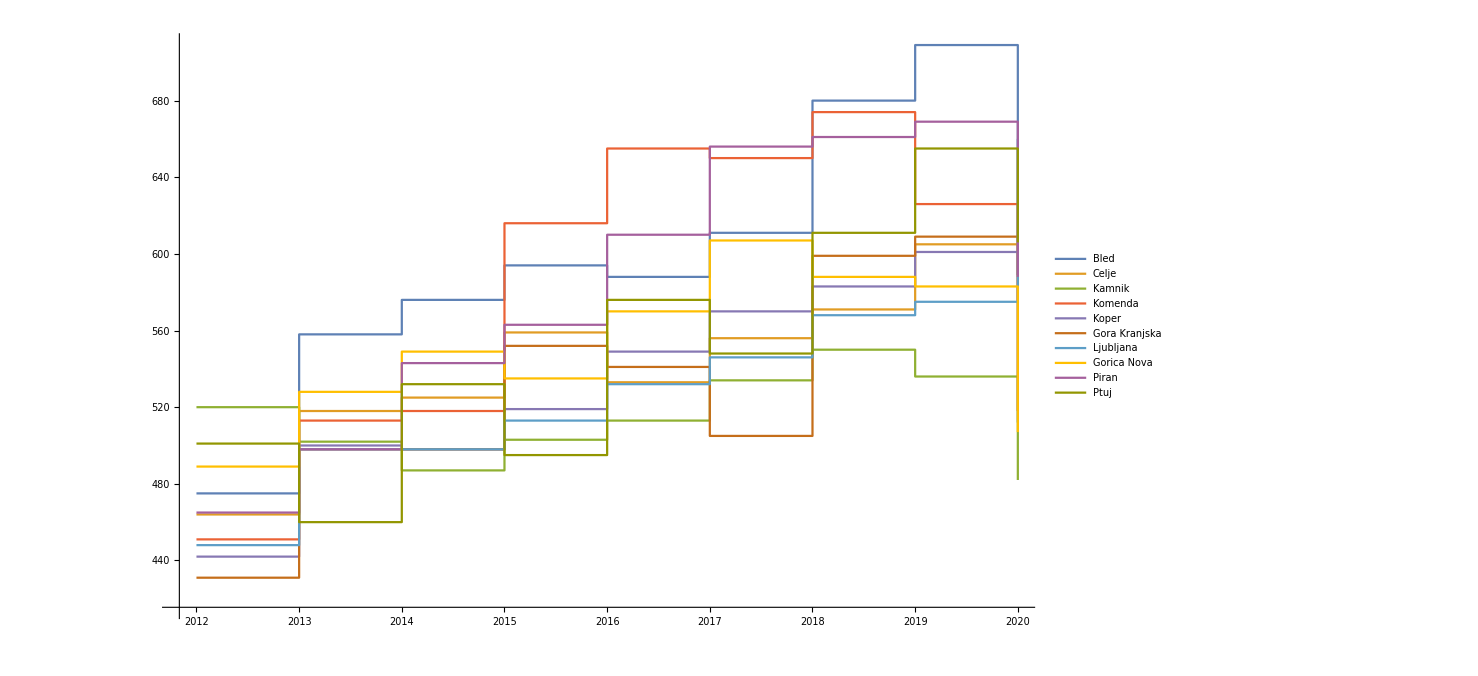

```mathematica
ListStepPlot[NastaliOdpadkiNajonesnazenih,PlotLegends->{Bled, Celje, Kamnik,Komenda, Koper, Kranjska Gora, Ljubljana, Nova Gorica, Piran, Ptuj}]
```

Podatke o prvih 10 najbolj onesnaženih občinah sem dobila tako, da sem seštela podatke o odloženih ter zbranih odpadkih za vsako občino med sabo in primerjala rezultate med seboj. Razlogi za veliko onesnaženost teh mest so različni. Za nekatere je velik razvita industrijska obrt ter razvito kmetijstvo. Brez dvoma pa lahko rečemo, da je najbolj problematičen dejavnik turizem, zato se na seznamu med prvimi pojavljajo Bled, Kranjska Gora, Ptuj, Ljubljana, Koper, Piran...